```mathematica
IncludeQuantities;

SetDirectory[ToString[NotebookDirectory[]]];
tabledata0=Import["DMS_Table.dat"];
tabledata1=Import["DMS_1u.txt","TSV"];
```

```mathematica
levels0=tabledata0⟦10⟧;
levelsX=tabledata0⟦11;;,2⟧;
```

Making the wavelength table (in nm) here:

```mathematica
lambdaTable0=Table[(14504.343+levels0⟦i0⟧-levelsX⟦iX⟧)^-1*10^7,{iX,Length[levelsX]},{i0,Length[levels0]}];
```

NOTE: 14504.343cm is the intercombination wavenumber. In the theoretical files levels0 and levelsX are default negative, which causes the unintuitive signs.

labels for the lambda plot including wavelengths already in the lab for producing Sr_2 molecules:

```mathematica
lbldcont={640,660,679.288,689.45,700,707.202,720,740,760,780,800};
```

```mathematica
labelPlot3=ListContourPlot[lambdaTable0,Contours->{640,650,660,670,679.288,689.45,700,707.202,720,730,740,750,760,770,780,790,800,810,820,830,840},Axes->True,ContourShading->None,ContourLabels->(If[MemberQ[lbldcont,#3],Text[#3,{#1,#2},Background->Transparent]]&),AspectRatio->.5];
```

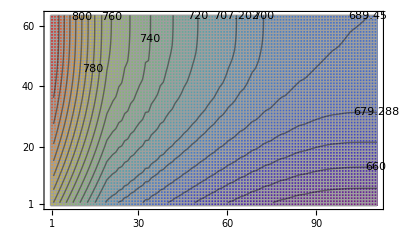

```mathematica
Show[ArrayPlot[lambdaTable0,PlotRange->{Min[lambdaTable0],Max[lambdaTable0]},FrameTicks->{{{1,10,20,30,40,50,60},False},{{1,10,20,30,40,50,60,70,80,90,100,110},False}},DataReversed->True,ColorFunction->"Rainbow",Mesh->True,Frame->True],labelPlot3]
```

Important!  The specification is lambdaTable⟦v,v’⟧ where v is the state label of the X (1S0-1S0 asymptote) potential and v’ is the state label of the 0 (3P0-1S0 asymptote) potential.  Negative numbers work here if you want to count from the least-bound state down (⟦-1,-3⟧ would be the least-bound state in the X potential to the third-from-most-weakly-bound state in the 0 potential), but be careful when counting from the bottom of the potential because Mathematica uses a first element is 1 counting system.  So if you want the nth state of the potential where n=0 is the lowest state, you have to put in e.g. ⟦1,-3⟧ (most deeply bound state in X to the third-most weakly bound 0 state).

Making the dms table...

```mathematica
dmsTable0=Drop[tabledata0,10,2];
```

Now, let’s repeat for the 1u levels.  We’ve already imported the table from Wotjek, but we have to finesse it a bit to get it in the same form as his 0u data.

```mathematica
levels1i=tabledata1⟦4,5;;⟧;
levelsX1i=tabledata1⟦7;;,3⟧;
```

Now to invert the ordering of the 1u levels since they’re backwards from the 0u table convention

```mathematica
levelsX1=Table[levelsX1i⟦i⟧,{i,Length[levelsX1i],1,-1}];
levels1=Table[levels1i⟦i⟧,{i,Length[levels1i],1,-1}];
lambdaTable1=Table[(14504.343+levels1⟦i1⟧-levelsX1⟦iX⟧)^-1*10^7,{iX,Length[levelsX1]},{i1,Length[levels1]}];
dmsTable1i=tabledata1⟦7;;,5;;⟧;
dmsTable1=Table[dmsTable1i⟦iX,i1⟧,{iX,Length[dmsTable1i],1,-1},{i1,Length[dmsTable1i⟦1⟧],1,-1}];
```

```mathematica
Convert[0.4/2.7(4×(dmsTable1⟦7,23⟧ (ElectronCharge BohrRadius)^2)/PlanckConstantReduced^2(2((200Milli Watt)/(π (30 Micro Meter)^2)))/(VacuumPermittivity SpeedOfLight)-(47Kilo Hertz)^2)/(2*47Kilo Hertz),Giga Hertz]
Convert[0.4/2.7((dmsTable0⟦7,-5⟧ (ElectronCharge BohrRadius)^2)/PlanckConstantReduced^2(2((30Micro Watt)/(π (50 Micro Meter)^2)))/(VacuumPermittivity SpeedOfLight)-(100Kilo Hertz)^2)/(2*100 Kilo Hertz),Mega Hertz]
Convert[0.4/2.7 Sqrt[4×(dmsTable1⟦7,23⟧ (ElectronCharge BohrRadius)^2)/PlanckConstantReduced^2(2((200Milli Watt)/(π (30 Micro Meter)^2)))/(VacuumPermittivity SpeedOfLight)],Mega Hertz]
Convert[0.4/2.7 Sqrt[(dmsTable0⟦7,-5⟧ (ElectronCharge BohrRadius)^2)/PlanckConstantReduced^2(2((310Micro Watt)/(π (100 Micro Meter)^2)))/(VacuumPermittivity SpeedOfLight)],Mega Hertz]
```

244.315 Giga Hertz

2.10207 Hertz Mega

58.3293 Hertz Mega

0.401829 Hertz Mega

```mathematica
Convert[SpeedOfLight/(905Nano Meter)-SpeedOfLight/(905.05Nano Meter),Giga Hertz]
```

18.3008 Giga Hertz

```mathematica
18/0.05/6
```

60.

```mathematica
4/27.
```

0.148148

```mathematica
(1/2 0.4/2.7)^0.5
```

0.272166

```mathematica
Convert[0.4/2.7((dmsTable1⟦7,23⟧ (ElectronCharge BohrRadius)^2)/PlanckConstantReduced^2(2((2*200Milli Watt)/(π (30 Micro Meter)^2)))/(VacuumPermittivity SpeedOfLight)-(47Kilo Hertz)^2)/(2*47Kilo Hertz),Giga Hertz]
```

122.157 Giga Hertz

```mathematica
State905with180MHz=Interval[{905.7000,906.6000}]; 
State912with180MHz=Interval[{912.102,912.2110}];
State905with35MHz=Interval[{905.5689,906.2725}];

State905with35MHzRange = ToString[QuantityMagnitude@UnitConvert[Quantity["SpeedOfLight"]]/Min[State905with35MHz]-QuantityMagnitude@UnitConvert[Quantity["SpeedOfLight"]]/Max[State905with35MHz]];

NumberLinePlot[{905.986,State905with35MHz,State905with180MHz},
Spacings-> {0,0.1,0.1},
PlotStyle->{Directive[Red,PointSize[Medium]],Directive[Blue,PointSize[0]],Directive[Green,PointSize[0]]},
PlotLegends->{"Crappy theory","0.0001nm steps (11/10~) " State905with35MHzRange"GHz covered.","0.0005nm stpes (11/8,9)"}]

NumberLinePlot[{905.986,912.101,918.299,State905with35MHz,State905with180MHz,State912with180MHz},
Spacings-> {0,0,0,0.1,0.1,0},
PlotStyle->{Directive[Red,PointSize[Medium]],Directive[Red,PointSize[Medium]],Directive[Red,PointSize[Medium]],
	              Directive[Blue,PointSize[0]],Directive[Green,PointSize[0]],Directive[Green,PointSize[0]]},
PlotLegends->{"Crappy theory",None,None,"0.0001nm steps (11/10~) " State905with35MHzRange"GHz covered.","0.0005nm stpes (11/8,9)"}]
```

NumberLinePlot[{905.986,Interval[{905.569,906.273}],Interval[{905.7,906.6}]},Spacings→{0,0.1,0.1},PlotStyle→{Directive[RGBColor[1,0,0],PointSize[Medium]],Directive[RGBColor[0,0,1],PointSize[0]],Directive[RGBColor[0,1,0],PointSize[0]]},PlotLegends→{Crappy theory,0.0001nm steps (11/10~)  257.02 GHz covered.,0.0005nm stpes (11/8,9)}]

NumberLinePlot[{905.986,912.101,918.299,Interval[{905.569,906.273}],Interval[{905.7,906.6}],Interval[{912.102,912.211}]},Spacings→{0,0,0,0.1,0.1,0},PlotStyle→{Directive[RGBColor[1,0,0],PointSize[Medium]],Directive[RGBColor[1,0,0],PointSize[Medium]],Directive[RGBColor[1,0,0],PointSize[Medium]],Directive[RGBColor[0,0,1],PointSize[0]],Directive[RGBColor[0,1,0],PointSize[0]],Directive[RGBColor[0,1,0],PointSize[0]]},PlotLegends→{Crappy theory,None,None,0.0001nm steps (11/10~)  257.02 GHz covered.,0.0005nm stpes (11/8,9)}]

```mathematica
NumberLinePlot[{905.986,State905with35MHz,State905with180MHz}]
```

NumberLinePlot[{905.986,Interval[{905.569,906.273}],Interval[{905.7,906.6}]}]

```mathematica
dmsTable1⟦7,23⟧
```

0.0001125

```mathematica
dmsTable0⟦-2,-5⟧
```

0.013765

The big numerator is the square of Rabi frequency. In dmsTable0⟦7,-5⟧ 7 means the 7th ground state counted from the bottom of ground state potential and -5 means the 5th excited state counted from the top of 0u excited potential. 1mW of 650E laser power and 50 microns beam waist are assumed. 90kHz is the experimental linwidth of X(-2,0) to 0u(-5,0) transition which is expected to be effected by 650E laser due to Autler-Townes splitting.

```mathematica
lambdaTable0[[1,14]]
```

723.765

```mathematica
Convert[SpeedOfLight*(1/(651.8659Nano Meter)-1/(651.8904Nano Meter)),Giga Hertz]
```

17.2844 Giga Hertz

```mathematica
Convert[Sqrt((dmsTable0⟦7,-5⟧ (ElectronCharge BohrRadius)^2)/PlanckConstantReduced^2(2((200Micro Watt)/(π (195Micro Meter)^2)))/(VacuumPermittivity SpeedOfLight))/1Mega Hertz,Mega Hertz]
```

Convert::incomp: Incompatible units in 1.24821×10^6\ Coulomb^2\ Hertz\ Mega\ Sqrt\ Volt\ Watt/Ampere\ Joule^2\ Micro\ Second^2 and Hertz\ Mega.

(1.24821×10^6 Coulomb^2 Hertz Mega Sqrt Volt Watt)/(Ampere Joule^2 Micro Second^2)

```mathematica
lambdaTable1[[-2,34]]
```

910.88

```mathematica
Convert[1/(3 π(SpeedOfLight)^3(PlanckConstantReduced )(VacuumPermittivity))(2π SpeedOfLight/(lambdaTable1⟦-2,34⟧Nano Meter))^3*dmsTable1⟦-2,34⟧(ElectronCharge BohrRadius)^2,Mega Hertz]
```

1.82168×10^-8 Hertz Mega

```mathematica
gamma0[i1_]:=Convert[Sum[1/(3 π(SpeedOfLight)^3(PlanckConstantReduced )(VacuumPermittivity))*( 2*Pi*SpeedOfLight/(lambdaTable0⟦iX,i1⟧Nano Meter))^3*dmsTable0⟦iX,i1⟧(ElectronCharge  BohrRadius)^2,{iX,Length[dmsTable0]}],Kilo Hertz];
```

```mathematica
gamma1[i1_]:=Convert[Sum[1/(3 π(SpeedOfLight)^3(PlanckConstantReduced )(VacuumPermittivity))(2π SpeedOfLight/(lambdaTable1⟦iX,i1⟧Nano Meter))^3*dmsTable1⟦iX,i1⟧(ElectronCharge BohrRadius)^2,{iX,Length[dmsTable1]}],Kilo Hertz];
```

```mathematica
gamma0[-1]
```

0.0118764 Hertz Kilo

```mathematica
gamma1[34]
```

3.81727 Hertz Kilo

```mathematica
lambdaTable0[[-2,-5]]
```

689.452

```mathematica
Convert[1/gamma0[-6],Second]
```

9.24591×10^-6 Second

```mathematica
{γ1=1.82*10^-8,γ2=3.8*10^-3,ω=1.2*10^9,ω0=2*10^9,p= 2.65}
```

{1.82×10^-8,0.0038,1.2×10^9,2000000000,2.65}